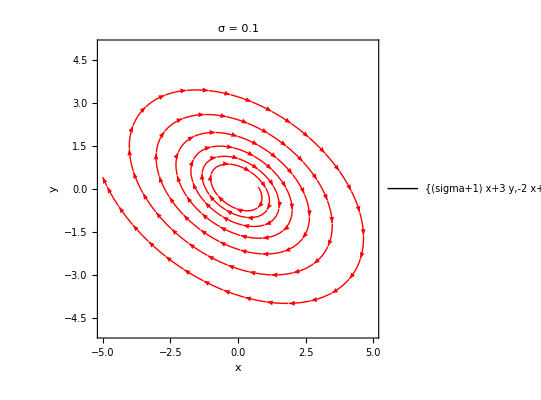

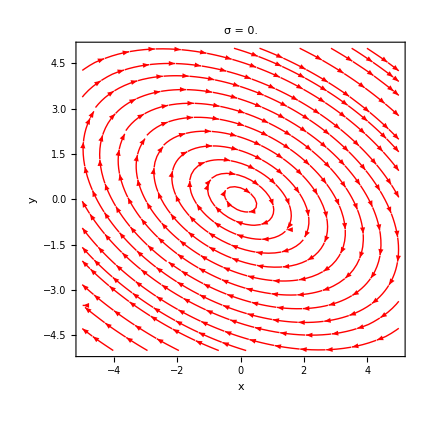

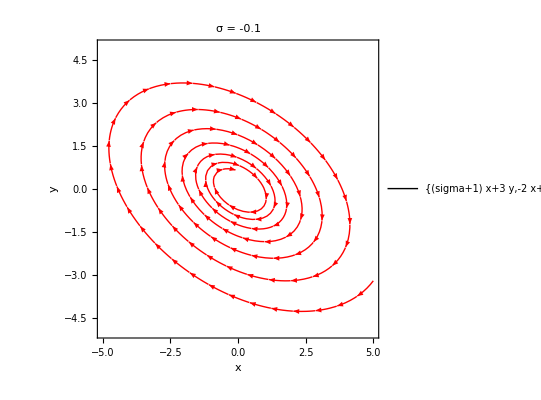

```mathematica
Clear[x,y, sigma, t, u, v];
sol = DSolve[{x'[t] == (sigma+1)*x[t] + 3*y[t], y'[t] == -2*x[t] + (sigma-1)*y[t],x[0] == u, y[0] == v},{x,y}, t];
x[t_] = x[t]/.sol;
y[t_] = y[t]/.sol;

sigma0 = 1/10;
StreamPlot[{(sigma +1)*x + 3y, -2x + (sigma-1)y}/.{sigma->sigma0}, {x, -5,5}, {y, -5,5},  PlotTheme -> "Detailed" , StreamStyle -> {Red},PlotLabel -> StringJoin["σ =  ", ToString[N[sigma0]]], StreamPoints -> {{{1, 2}, Red}}, FrameLabel->{Style["x",Black,Medium],Style["y",Black,Medium]}]

sigma0 = 0;
StreamPlot[{(sigma +1)*x + 3y, -2x + (sigma-1)y}/.{sigma->sigma0}, {x, -5,5}, {y, -5,5},  PlotTheme -> "Sparse" , StreamStyle -> {Red},PlotLabel -> StringJoin["σ =  ", ToString[N[sigma0]]], FrameLabel->{Style["x",Black,Medium],Style["y",Black,Medium]}]

sigma0 = -1/10;
StreamPlot[{(sigma +1)*x + 3y, -2x + (sigma-1)y}/.{sigma->sigma0}, {x, -5,5}, {y, -5,5},  PlotTheme -> "Detailed" , StreamStyle -> {Red},PlotLabel -> StringJoin["σ =  ", ToString[N[sigma0]]], StreamPoints -> {{{1, 2}, Red}}, FrameLabel->{Style["x",Black,Medium],Style["y",Black,Medium]}]
```

```mathematica
x[t_] = x[t]/.{sigma->0};
y[t_] = y[t]/.{sigma->0};
Manipulate[ParametricPlot[{x[t],y[t]}/.{ u->u0, v->v0}, {t,0,10}, PlotRange -> {{-5, 5},{-5,5}}],  {u0, 0, 5}, {v0, 0, 5}]
```

```mathematica
u0 = 1;
v0 = 1;
f[t_] = x[t]/.{sigma -> 0, u->u0, v->v0};
g[t_] = y[t]/.{sigma -> 0, u->u0, v->v0};
FullSimplify[Maximize[Sqrt[f[t]^2 + g[t]^2], t]/Minimize[Sqrt[f[t]^2 + g[t]^2], t]]:

nm = FullSimplify[Maximize[Sqrt[f[t]^2 + g[t]^2], t]];
t0 = t /. Last[nm];
v = {f[t0], g[t0]};
```

```mathematica
b= FullSimplify[v];
b= {b[[1]][[1]], b[[2]][[1]]};
c = Normalize[-b];
Simplify[c]
```

{-v/(√2 Abs[v]),-v/(√2 Abs[v])}